## 1.1.8 Интерполяционная формула Ньютона в начале таблицы

### Выполнил Ерофеевский Александр

Дано: таблица точек и значений функции

```mathematica
Clear@NewtonInterpolation
NewtonInterpolation[points_,temp_,grad_]:=
Module[{f,x,dy,p,h=points⟦1,2⟧-points⟦1,1⟧,t},
Do[x[i-1]=points⟦1,i⟧;
f[x[i-1]]=points⟦2,i⟧,
{i,Length@points⟦1⟧}];
dy[x_,1]:=f[x+h]-f[x];
dy[x_,k_]:=dy[x+h,k-1]-dy[x,k-1];
t[y_]:=(y-x[0])/h;
p[y_,n_]:=f[x[0]]+Sum[(Times@@Table[(t[y]-j),{j,0,i-1}])*dy[x[0],i]/Factorial[i],{i,1,n}];
p[temp,grad]
]
```

Результаты

Возьмем несколько значений функции

```mathematica
f[x_]:=x^3-0.2 x^2-0.2x-1.2
```

```mathematica
Clear@interPoint
(interPoint={Table[x,{x,1,4}],Table[f[x],{x,1,4}]})//TableForm
```

1 | 2 | 3 | 4
-0.6 | 5.6 | 23.4 | 58.8

```mathematica
NewtonInterpolation[interPoint,x,3]
```

-0.6+6.2 (-1+x)+5.8 (-2+x) (-1+x)+1. (-3+x) (-2+x) (-1+x)

Проверка

```mathematica
Table[NewtonInterpolation[interPoint,i,3]==f[i],{i,6}]
```

{True,True,True,True,True,True}

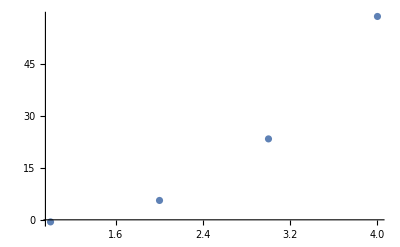

```mathematica
ListPlot[interPoint⟦2⟧,DataRange->{interPoint⟦1,1⟧,interPoint⟦1,-1⟧}]
```

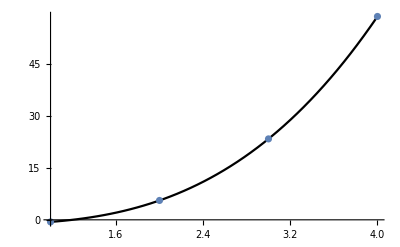

```mathematica
Show[Plot[NewtonInterpolation[interPoint,x,3],{x,interPoint⟦1,1⟧,interPoint⟦1,-1⟧},PlotStyle->Black],ListPlot[interPoint⟦2⟧,DataRange->{interPoint⟦1,1⟧,interPoint⟦1,-1⟧}]]
```

Пример 2

```mathematica
f2[x_]:=x^4+3 x^3-11 x^2-3x+10
```

```mathematica
(interPoint2={Table[x,{x,-15,14,6}],Table[f2[x],{x,-15,14,6}]})//TableForm
```

-15 | -9 | -3 | 3 | 9
38080 | 3520 | -80 | 64 | 7840

```mathematica
NewtonInterpolation[interPoint2,x,4]
```

38080-5760 (15+x)+2580 (15+x) (-1+(15+x)/6)-756 (15+x) (-2+(15+x)/6) (-1+(15+x)/6)+216 (15+x) (-3+(15+x)/6) (-2+(15+x)/6) (-1+(15+x)/6)

Проверка

```mathematica
Table[NewtonInterpolation[interPoint2,i,4]==f2[i],{i,1,9,2}]
```

{True,True,True,True,True}

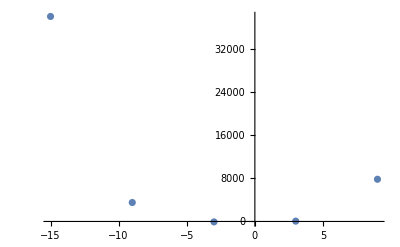

```mathematica
ListPlot[interPoint2⟦2⟧,DataRange->{interPoint2⟦1,1⟧,interPoint2⟦1,-1⟧}]
```

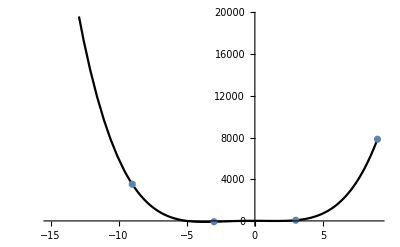

```mathematica
Show[Plot[NewtonInterpolation[interPoint2,x,4],{x,interPoint2⟦1,1⟧,interPoint2⟦1,-1⟧},PlotStyle->Black],ListPlot[interPoint2⟦2⟧,DataRange->{interPoint2⟦1,1⟧,interPoint2⟦1,-1⟧}]]
```